```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./LPAp_mub0/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub0/buffer/Zphi.dat"]];
T0=Flatten[Import["./LPAp_mub0/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub0linear=Transpose[{T0[[2;;Length[t]-2]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["./LPAp_mub50/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub50/buffer/Zphi.dat"]];
T=Flatten[Import["./LPAp_mub50/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub50=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
b1mub50linear=Transpose[{T[[2;;Length[t]-2]],-Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];


fpi=Flatten[Import["./LPAp_mub100/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub100/buffer/Zphi.dat"]];
T100=Flatten[Import["./LPAp_mub100/buffer/TMeV.dat"]];
t=-(T100-T100[[1]])/T100[[1]];
datamub100=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]*√Zphi[[2;;Length[t]]]]}];
b1mub100=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub100[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T100]-2}]]}];
b1mub100linear=Transpose[{T100[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub100[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T100]-2}]]}];

fpi=Flatten[Import["./LPAp_mub150/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub150/buffer/Zphi.dat"]];
T=Flatten[Import["./LPAp_mub150/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub150=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
b1mub150linear=Transpose[{T[[2;;Length[t]-2]],-Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];


fpi=Flatten[Import["./LPAp_mub200/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub200/buffer/Zphi.dat"]];
T200=Flatten[Import["./LPAp_mub200/buffer/TMeV.dat"]];
t=-(T200-T200[[1]])/T200[[1]];
datamub200=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]*√Zphi[[2;;Length[t]]]]}];
b1mub200=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub200[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T200]-2}]]}];
b1mub200linear=Transpose[{T200[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub200[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T200]-2}]]}];

fpi=Flatten[Import["./LPAp_mub250/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub250/buffer/Zphi.dat"]];
T=Flatten[Import["./LPAp_mub250/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub250=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
b1mub250linear=Transpose[{T[[2;;Length[t]-2]],-Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];


fpi=Flatten[Import["./LPAp_mub300/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub300/buffer/Zphi.dat"]];
T300=Flatten[Import["./LPAp_mub300/buffer/TMeV.dat"]];
t=-(T300-T300[[1]])/T300[[1]];
datamub300=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]*√Zphi[[2;;Length[t]]]]}];
b1mub300=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];
b1mub300linear=Transpose[{T300[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];

fpi=Flatten[Import["./LPAp_mub350/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub350/buffer/Zphi.dat"]];
T=Flatten[Import["./LPAp_mub350/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub350=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
b1mub350linear=Transpose[{T[[2;;Length[t]-2]],-Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];


fpi=Flatten[Import["./LPAp_mub400/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub400/buffer/Zphi.dat"]];
T400=Flatten[Import["./LPAp_mub400/buffer/TMeV.dat"]];
t=-(T400-T400[[1]])/T400[[1]];
datamub400=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]*√Zphi[[2;;Length[t]]]]}];
b1mub400=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];
b1mub400linear=Transpose[{T400[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];

fpi=Flatten[Import["./LPAp_mub450/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub450/buffer/Zphi.dat"]];
T450=Flatten[Import["./LPAp_mub450/buffer/TMeV.dat"]];
t=-(T450-T450[[1]])/T450[[1]];
datamub450=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]*√Zphi[[2;;Length[t]]]]}];
b1mub450=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub450[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T450]-2}]]}];
b1mub450linear=Transpose[{T450[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub450[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T450]-2}]]}];

fpi=Flatten[Import["./LPAp_mub475/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub475/buffer/Zphi.dat"]];
T=Flatten[Import["./LPAp_mub475/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub475=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
b1mub475linear=Transpose[{T[[2;;Length[t]-2]],-Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];


fpi=Flatten[Import["./LPAp_mub500/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub500/buffer/Zphi.dat"]];
T500=Flatten[Import["./LPAp_mub500/buffer/TMeV.dat"]];
t=-(T500-T500[[1]])/T500[[1]];
datamub500=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]*√Zphi[[2;;Length[t]]]]}];
b1mub500=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];
b1mub500linear=Transpose[{T500[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];

fpi=Flatten[Import["./LPAp_mub530/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub530/buffer/Zphi.dat"]];
T530=Flatten[Import["./LPAp_mub530/buffer/TMeV.dat"]];
t=-(T530-T530[[1]])/T530[[1]];
datamub530=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]*√Zphi[[2;;Length[t]]]]}];
b1mub530=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub530[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T530]-2}]]}];
b1mub530linear=Transpose[{T530[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub530[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T530]-2}]]}];
```

## Plot

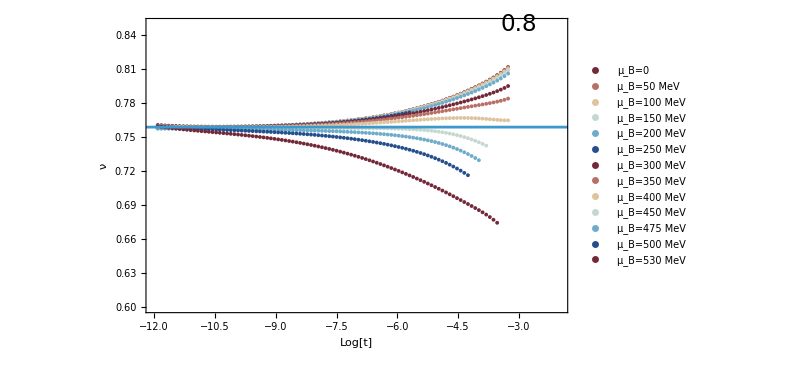

```mathematica
plotT=Show[ListPlot[{Re[b1mub0],Re[b1mub50],Re[b1mub100],Re[b1mub150],Re[b1mub200],Re[b1mub250],Re[b1mub300],Re[b1mub350],Re[b1mub400],Re[b1mub450],Re[b1mub475],Re[b1mub500],Re[b1mub530]},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.2}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0","μ_B=50 MeV","μ_B=100 MeV","μ_B=150 MeV","μ_B=200 MeV","μ_B=250 MeV","μ_B=300 MeV","μ_B=350 MeV","μ_B=400 MeV","μ_B=450 MeV","μ_B=475 MeV","μ_B=500 MeV","μ_B=530 MeV"},LabelStyle->16],{0.23,0.32}],
PlotRange->{{-12,-2},{0.6,0.85}},AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.759},{10,0.759}}],ImageSize->600,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.85}]}]
```

```mathematica
Export["./LOdata/mub0data.dat",b1mub0];
Export["./LOdata/mub100data.dat",b1mub100];Export["./LOdata/mub200data.dat",b1mub200];Export["./LOdata/mub300data.dat",b1mub300];
Export["./LOdata/mub400data.dat",b1mub400];
Export["./LOdata/mub450data.dat",b1mub450];
Export["./LOdata/mub500data.dat",b1mub500];
Export["./LOdata/mub530data.dat",b1mub530];
```

```mathematica
Export["./2Ddata/mub0data.dat",b1mub0linear];
Export["./2Ddata/mub50data.dat",b1mub50linear];
Export["./2Ddata/mub100data.dat",b1mub100linear];
Export["./2Ddata/mub150data.dat",b1mub150linear];
Export["./2Ddata/mub200data.dat",b1mub200linear];
Export["./2Ddata/mub250data.dat",b1mub250linear];
Export["./2Ddata/mub300data.dat",b1mub300linear];
Export["./2Ddata/mub350data.dat",b1mub350linear];
Export["./2Ddata/mub400data.dat",b1mub400linear];
Export["./2Ddata/mub450data.dat",b1mub450linear];
Export["./2Ddata/mub475data.dat",b1mub475linear];
Export["./2Ddata/mub500data.dat",b1mub500linear];
Export["./2Ddata/mub530data.dat",b1mub530linear];
```